# CervicalCheck data (2008-2022) -Graphics--Graphics-

-Graphics--Graphics-
The above are the relevant tables from cervical check reports 1 and 2. We do the same analysis, only now we factor out recalled cases so we don't double count!

{0.000000.00013,11.6.,13.7.,23.13.,18.9.,14.8.,17.9.,22.12.,25.14.,29.15.,33.18.,45.24.,28.15.,33.18.,60.32.}

{0.00000.0004,70.31.,69.31.,106.47.,66.30.,48.22.,54.24.,62.28.,78.35.,76.34.,73.33.,75.34.,47.21.,49.22.,99.44.}

{0.00000.0016,305.111.,303.110.,463.169.,289.105.,210.77.,234.85.,271.99.,342.125.,330.120.,318.116.,328.119.,205.75.,213.78.,433.158.}

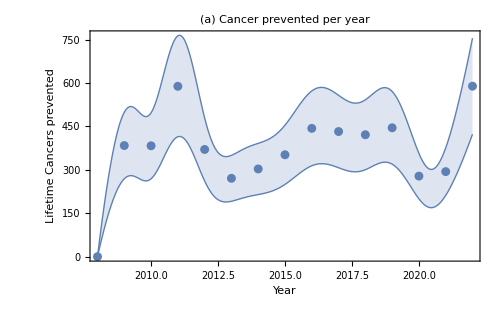
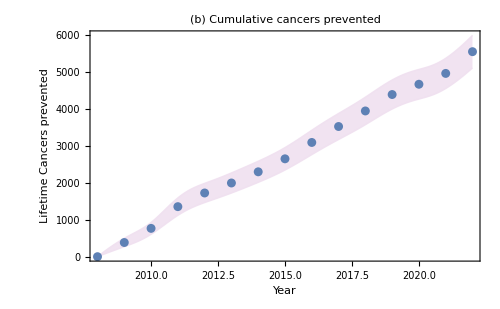

Average lifetime cancers prevented per year: 382.30.

382.30.

```mathematica
year = Table[i,{i,2008,2022}];
(*Total CIN1 / HSIL cases handled that year*)
cin1total={Around[0,0.01],1652,2947,3939,4885,4334,4658,5618,6217,6263,6702,8357,5078,6954,9692};
hsiltotal={Around[0,0.01],3648,5379,6343,6508,5261,5265,5741,6786,5853,5231,5010,3085,3602,5693};

(*New to review ratio (only consider new cases, presume we can only prevent cancer ONCE)*)
newrecallratio = 1+{0,0.91,1.84,1.19,2.6,3,2.59,2.39,2.17,1.83,1.63,1.44,1.4,1.7,1.1};
cin1 = cin1total/newrecallratio;
hsil = hsiltotal/newrecallratio;

(*Cancers detected by screening and NCRI in total*)
cancersscreen = {0,99,184,222,185,158,177,170,174,124,119,100,74,79,108};
cancerstotal = {264,356,338,336,300,286,281,248,291,294,303,266,193,303,250};

(*Ratio of CIN1/2 cases*)
pc2=Around[0.4814,0.011];
pc3=Around[0.5186,0.011];
cin2=pc2*hsil;
cin3=pc3*hsil;

(*Transition probabilities for model 3*)
cc1m3=Around[0.013,0.007];
cc2m3=Around[0.076,0.034];
cc3m3=Around[0.308,0.112];

cin1prevm3 = cin1*cc1m3
cin2prevm3 = cin2*cc2m3
cin3prevm3 = cin3*cc3m3

eff = Around[0.993,0.004];

(*Total prevented that year over a lifetime... *)
totalm3 = cin1prevm3 + cin2prevm3 + eff*cin3prevm3;
cumversion = Accumulate[totalm3];
combinedlist = Transpose[{year,totalm3}];
combinedlist2 = Transpose[{year,cumversion}];
aplot = ListPlot[combinedlist,IntervalMarkers->"Bands",InterpolationOrder->5,PlotRange->All,
Frame->{True,True,False,False},FrameLabel->{"Year","Lifetime Cancers prevented"},
PlotLabel->"(a) Cancer prevented per year ",ImageSize->500];
bplot = ListPlot[combinedlist2,IntervalMarkersStyle -> Directive[LightPurple, Opacity[0.9]],
IntervalMarkers->"Bands",InterpolationOrder->5,PlotRange->All,Frame->{True,True,False,False},
FrameLabel->{"Year","Lifetime Cancers prevented"},PlotLabel->"(b) Cumulative cancers prevented",ImageSize->500];
Row[{aplot,bplot}]

(*Quick calculation to work out annual cancers prevented*)
timetotal = 13 + 7/12;
totalpre = (Mean[totalm3]*14)/timetotal;

TextCell[formattedText = Row[{
  "Average lifetime cancers prevented per year: ", 
  totalpre
}],"Text"]


timetotal = 13 + 7/12;
totalpre = (Mean[totalm3]*14)/timetotal
```

```mathematica
(*Also, let's work out the cancer prevented per 1000 screened based on UNIQUE screenings! *)
yearsunique = Table[i,{i,2017,2022,1}];
uniqueprevents = Table[totalm3[[i]],{i,10,15}];
uniquescreens = {355353,257449,121269,216471,310345};
preper1000 = 1000*Total[uniqueprevents]/(Total[uniquescreens]);
(*Just a graph of proportion of screening detected cancers versus non-screening detected! *)
proportionscreened = cancersscreen/cancerstotal;

(* Use BarChart*)
barChart = BarChart[100*proportionscreened, 
  ChartLabels -> {year}, (* Add year labels *)
  ChartStyle -> "Pastel", (* Set chart style *)
  PlotTheme -> "Marketing", (* Set plot theme *)
  ImageSize -> 800, (* Set image size *)
  FrameLabel -> {"Year", "Proportion (%)"} (* Add axis labels *)
];

TextCell[formattedText = Row[{
  "Cancers prevented per 1000 screens: ", 
 preper1000
}],"Text"]
```

Cancers prevented per 1000 screens: 1.950.23

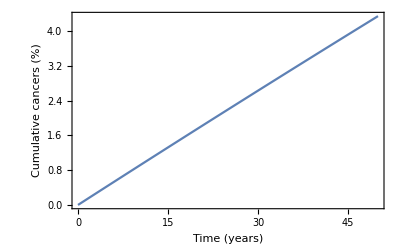

```mathematica
(*In this section, we can also check the exponential distribution part of the paper! From literature, we know: 0.62% of women with LG have a cancer after 7 years.
Let's presume exp. distribution, of form: CDF(t) = 1 - exp(-λt) - therefore, we estimate parameter by*)

λ=N[-Log[1 - 62/10000]/7];

(*median time to cancer from low grade is 21 years in lit, thus from expo dist, mean time is 30.3:*)
meantime = N[21/Log[2]];
meancancerlg = 1 - Exp[-meantime*λ];
medcancerlg = 1 - Exp[-21*λ];

Plot[100*(1-Exp[-λ*x]),{x,0,50},Frame->True,FrameLabel->{"Time (years)","Cumulative cancers (%)"}]
```